```mathematica
xIn[size_]:=Function[x,Array[{x,#}&,size]]/@Range[size]
```

```mathematica
basicPlaneList[cx_,cy_,w_,t_,size_]:=Graphics[{Raster[(xIn[size]/.{x_,y_}:>{1,Norm[{Cos[cx*x-w*t],Cos[cy*y-w*t]}],0})],Disk[{#[[2]],#[[1]]}+{Cos[cy*#[[2]]-w*t],Cos[cx*#[[1]]-w*t]},.25]&/@Flatten[xIn[size],1]}]
```

```mathematica
basicTransverseList[cx_,cy_,w_,t_,size_]:=Graphics[{Raster[(xIn[size]/.{x_,y_}:>{1,Norm[{Cos[cy*x-w*t],Cos[cx*y-w*t]}],0})],Disk[{#[[1]],#[[2]]}+{Cos[cy*#[[2]]-w*t],Cos[cx*#[[1]]-w*t]},.25]&/@Flatten[xIn[size],1]}]
```

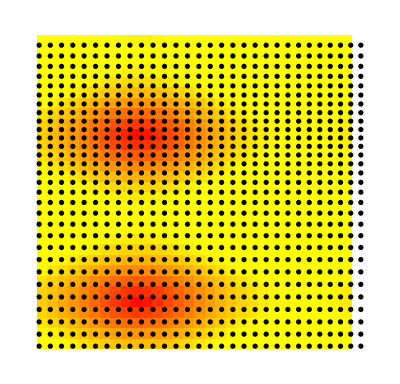
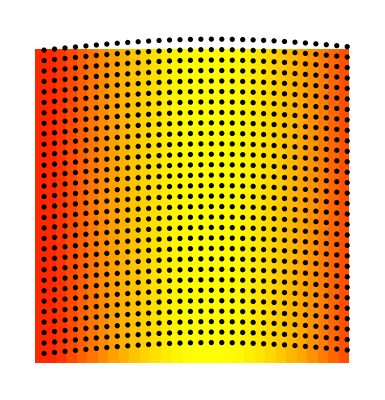

```mathematica
(*Change the parameters of these functions to change the graphs*)
{basicPlaneList[.2,.1,1,2.6,30],basicTransverseList[.1,0,2,4,30]}
```

```mathematica
(*This function creates an animated version of on e of the above waves, using the same parameters. The "type" parameter should be long or trans.*)
animateWave[cx_,cy_,w_,size_,type_]:=If[type===long,
Animate[basicPlaneList[cx,cy,w,t,size],{t,0,2*Pi/w}],
Animate[basicTransverseList[cx,cy,w,t,size],{t,0,2*Pi/w}]]
```

```mathematica
animateWave[.1,0,.2,30,long]
```